```mathematica
SetDirectory[NotebookDirectory[]]
matrixDir = Directory[]<>"/Mueller_AR/";
mueller8 = Import[matrixDir<>"Mueller_V2_nu90.0_no3p068_ne3p402_ARcoat_thetain8.0.txt", "Table"];
mueller10 = Import[matrixDir<>"Mueller_V2_nu90.0_no3p068_ne3p402_ARcoat_thetain10.0.txt", "Table"];
mueller15 = Import[matrixDir<>"Mueller_V2_nu90.0_no3p068_ne3p402_ARcoat_thetain15.0.txt", "Table"];
```

/Users/jacoblashner/so/lab_analysis/apps/4f_model

```mathematica
bc = 93*^9;
fbw = .376;
flo = bc * (1 - .5 * fbw);
fhi = bc * (1 + .5 * fbw);
```

```mathematica
data = {{mueller8⟦2;;,1⟧, mueller8⟦2;;,3⟧}ᵀ,
{mueller10⟦2;;,1⟧, mueller10⟦2;;,3⟧}ᵀ,
{mueller15⟦2;;,1⟧, mueller15⟦2;;,3⟧}ᵀ};
```

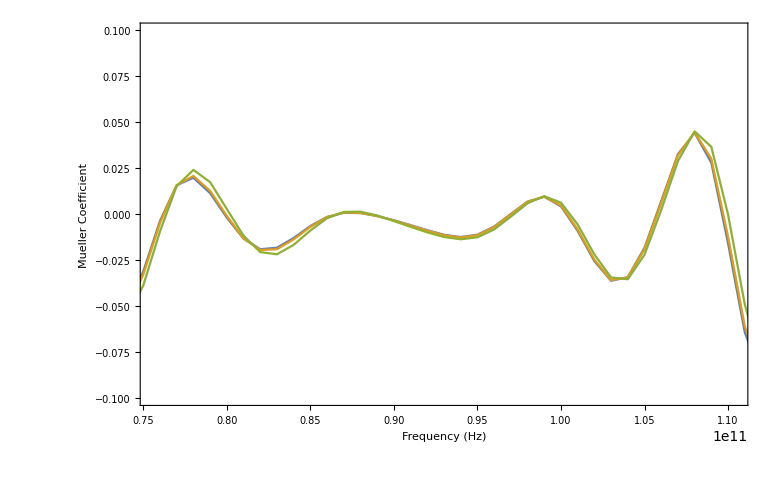

```mathematica
ListLinePlot[data, PlotRange->{{flo, fhi}, {-.1, .1}},
Frame->{True,True,False,False},
FrameLabel->{Style["Frequency (Hz)", FontSize->15, FontFamily->"Times"],Style["Mueller Coefficient", FontSize->15, FontFamily->"Times"]}]
```